# Clase 0: Introducción al Lenguaje

Tomás de Camino Beck, Ph.D.

Introducción a las funciones básicas de Mathematica

## Inducción

### Actividades Instigadoras

¿Cómo interpretaría usted estas líneas de código:

{1,2,3,4,5}

## Discusión: Operaciones Aritméticas con Mathematica

#### Primeros pasos

Las operaciones se aplican como cualquier otro lenguaje:

```mathematica
3+4
```

7

```mathematica
(3+5)/2 (7-2)
```

20

Noten como la multiplicación no necesita simbolo en esa expresión.

Una ventaja de Mathematica ers que este lenguaje es funcional y puede manipular símbolos, entonces una operación algebráica, es interpretada correctamente por el lenguaje:

```mathematica
x + x
```

2 x

```mathematica
x x
```

x^2

```mathematica
x^-1
```

1/x

De hecho podemos ver los árboles de expresión que se generan:

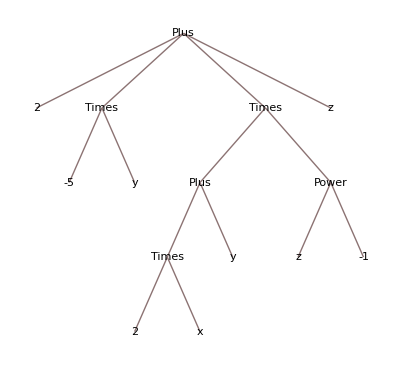

```mathematica
TreeForm[(2x+y)/z+z+2-5y]
```

La función TreeForm[], genera el árbol de expresión que intuitivamente se evalúa de abajo hacia arriba (de las hojas a la raíz)

Aunque Mathematica interpreta notación estándar matemática como la anterior, internamente todo es una expresión “`refija”, y esa expresión simepre es una función.  Por ejemplo:

```mathematica
Plus[x,y]
```

x+y

Noten como en realidad la operación “+“ es la funcón Plus[], y de hecho esta función puede evaluar una secuencia completa,

```mathematica
Plus[x,y,z,r,t]
```

r+t+x+y+z

Entonces, todo en matemática es una expresión del tipo

Head[elem_1,elem_2,elem_3,…]

Donde Head es una función que se aplica a una secuencia de elementos, como en el ejemplo de la función Plus[].  Para ver internamente cual es la forma funcional de matemática de cualquier expresión, podemos utilizar la función FullForm[],

```mathematica
FullForm[(2x+y)/z+z+2-5y]
```

Plus[2,Times[-5,y],Times[Plus[Times[2,x],y],Power[z,-1]],z]

Noten como todos los operadores son funciones que se aplican de forma compuesta (funciones dentro de funciones)

De todas maneras, lo recomendado es utilizar la notación estándar para operaciónes aritméticas conocidas, luego hablarémos un poco más de lenguajes funcionales y como funciona matemática

De hecho se puede ver que función define una celda utilizando la función Head[]:

```mathematica
Head[3]
```

Integer

```mathematica
Head[x]
```

Symbol

```mathematica
Head[True]
```

Symbol

```mathematica
Head[3x + y]
```

Plus

#### Graficando funciones

Una de las funciones de gran utilidad de mathematica es la de graficar cualqueir función o conjunto de datos:

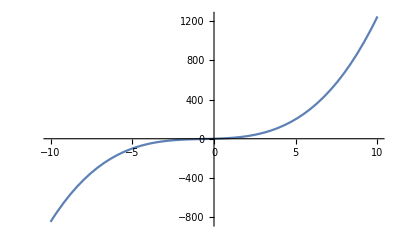

```mathematica
Plot[x^3+2 x^2+5x,{x,-10,10}]
```

Noten como la función se define simbólicamente, y simplemente se define el rango que querémos graficar (en el ejemplo con  de -10 a 10).

Mathematica tiene muchos tipos de gráfico, que más adelante exploraremos, esto incluye gráficos en 3 dimensiones:

```mathematica
Plot3D[Cos[x^2+y^2],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

Pueden ver más tipos de gráficos de funciones en esta dirección (allí se incluyen montones de ejemplos): 
["http://reference.wolfram.com/language/guide/FunctionVisualization.html"](http://reference.wolfram.com/language/guide/FunctionVisualization.html)

#### Listas (tablas y arreglos)

En un lenguaje funcional como Mathematica, las listas son extremadamente importantes. Las listas son equivalentes (pero no necesariemente iguales), a los arreglos en otros lenguajes de programación.

Una lista es una función List[] que contiene una secuencia de elementos:

```mathematica
List[a,b,c,d,e]
```

{a,b,c,d,e}

```mathematica
List[1,2,3,4,5]
```

{1,2,3,4,5}

```mathematica
List[a,v,1,3,"Hola"]
```

{a,v,1,3,Hola}

Noten como esa secuencia de elementos pueden ser de cualquier tipo, y pueden ser combinadas.

En Mathematica, se pueden construir listas ya sea con la función List[] como en los ejemplos anteriores, pero también solamente utilizando los corchetes {}, el resultado es el mismo

```mathematica
{a,b,c,d,e}
```

{a,b,c,d,e}

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{a,v,1,3,"Hola"}
```

{a,v,1,3,Hola}

Vea si por ejemplo los comparamos (utilizamos “===”)

```mathematica
{a,b,c,d,e}===List[a,b,c,d,e]
```

True

El operador “===” es la versión en notación estándar de SameQ[],

```mathematica
SameQ[{a,b,c,d,e},List[a,b,c,d,e]]
```

True

Noten que esta última correpodne a la notación de función (encabezado seguido de secuencia de elementos).

También se pueden construir listas con otras funciones que facilitan el trabajo, por ejemplo:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

O la función Table[], que utilizaremos mucho en el curso,

```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

Noten como ambas funciones ehacen lo mismo, pero Table[], permite construir listas más complejas. ¿Podría interpretar lo que significa la línea de código Table[2 i,{i,1,10}]?

Esa forma de construir listas, utiliza un iterador, que en e ejemplo llamamos i.  En lenguajes funcionales, no hay ciclos de control como los de lenguajes Python o Java, sino funciones iterables como Table[]. Así por ejemplo en Python, para construir un lista de números múltiplos de 2, tendríamos algo como:

numbers = []
for i in range(1, 10):
  numbers.append(2*i)
print(numbers)

El resultado sería [2, 4, 6, 8, 10, 12, 14, 16, 18]. En Mathematica sería,

```mathematica
Table[2 i,{i,1,10}]
```

{2,4,6,8,10,12,14,16,18,20}

Noten que se genera la lista a partir de una función que “itera”, sin necesidad de utilizar ciclos de control

#### Asignación de variables

Los valores se pueden asignar utiizando el símbolo “=”:

```mathematica
x = 10
```

10

Si evalúo la expresión x, obtengo el valor 10,

```mathematica
x
```

10

Para borrar las asignaciones se utiliza “=.”. Luego, si evalúo, “x” es solamente un símbolo

```mathematica
x =.
```

```mathematica
x
```

x

Se puede asignar una lista:

```mathematica
numbers=Table[2 i,{i,1,10}]
```

{2,4,6,8,10,12,14,16,18,20}

Por ejemplo ahora toda la lista se puede dividir entre 2,

```mathematica
numbers / 2
```

{1,2,3,4,5,6,7,8,9,10}

Hasta gráficos pueden ser asignados.  Por ejemplo grafiquemos la lista de números que acabamos de construir:

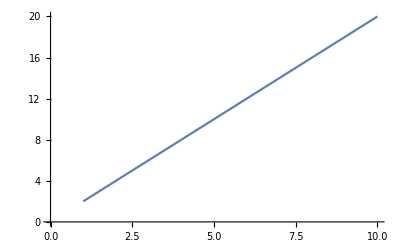

```mathematica
plot1=ListLinePlot[numbers]
```

Asignamos el gráfico a la variable plot1.  ahora la podemos volver a evaluar,

```mathematica
plot1
```

-Graphics-

Todo es “asignable” en Mathematica. Hay otras formas de asignar como la de otros lenguajes de programación (+=, -=, *=, /=), y otras propias de lenguaje funcional que discutiremos más adelante cuando hablemos de lenguajes funcionales

## Ejercicios

Para estos ejercicios, utilice la opción de ingreso libre de texto, y la ayuda de Mathematica . En cada uno
de los ejercicios, no solamente resuelva, sino explique en un texto de un párrafo, cada uno de los
elementos del cálculo . Los ejercicios son simples, la intención es buscar una excusa para aplicar difer .02entes funciones y además entender el funcionamiento de Mathematica

Imprima "Hola, mundo" en la consola de Mathematica .

Calcule el valor de pi utilizando la función N[Pi] .

Resuelva la ecuación x^2 + 2 x - 3 = 0 utilizando la función Solve[] .

Grafique la función y = x^2 en el intervalo[-10, 10] .

Utilice la función Sum[] para calcular la sumatoria de los números del 1 al 100.

Utilice la función Product[] para calcular el producto de los números del 1 al 10.

Utilice la función Table[] para generar una tabla de valores de la función y = x^2 para x = 1, 2, 3, ..., 10.

Utilice la función Plot3D[] para generar un gráfico tridimensional de la función z = x^2 + y^2.

Utilice la función Limit[] para calcular el límite de la función y = x^2 cuando x se acerca a 0.

Utilice la función Simplify[] para simplificar la expresión (x^2 + 2 x + 1)/(x^2 + x - 2) .

Utilice la función Factor[] para factorizar la expresión x^2 + 2 x + 1.

Utilice la función Solve[] para resolver la ecuación x^3 + 4 x^2 + 4 x - 8 = 0.

Utilice la función FindRoot[] para encontrar la raíz de la ecuación x^3 - 2 x - 5 = 0.

Utilice la función MatrixForm[] para imprimir una matriz de 3 x3 en formato matricial .

Utilice la función Inverse[] para calcular la inversa de una matriz de 3 x3 .

## Material Extra

Video: Uso de Cuadrenos Computacionales
https://drive.google.com/file/d/1Fg18ZAnxI3CjVdhjbKOk086SGXL3O6cF/view?usp=share_link

Introducción rápida para programadores (no es tan buena, pero sirve): https://www.wolfram.com/language/fast-introduction-for-programmers/es/

Todo el material que preparo para el curso, está fuertemente basado (adaptado a Mathematica) en este libro de Fenton & Dubinsky: https://drive.google.com/file/d/1HOZg2wcrS3mDQkTcCsmMblTZJFXpMg6f/view?usp=share_link

Video del creador de Mathematica Stephen Wolfram, explicando que es Mathematica https://youtu.be/L7MiE1zO5PI